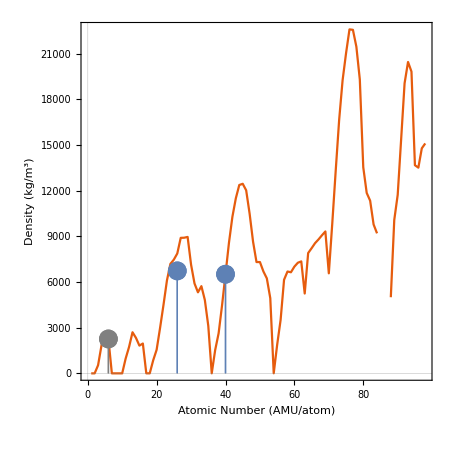

```mathematica
Show[{ListLinePlot[Table[ElementData[z,"Density"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,Black],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom)",20,Black],Style["Density (kg/m^3)",20,Black]},ImageSize->450,AspectRatio->1],ListPlot[Table[{z,ElementData[z,"Density"]},{z,6,6}],PlotStyle->Directive[Gray,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[Table[{z,ElementData[z,"Density"]},{z,40,40}],PlotStyle->Directive[PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[{{(12+40)/2,6.73*10^3}},PlotStyle->Directive[PointSize[0.03]],Filling->Bottom,FillingStyle->Thick]}]
```

```mathematica
Show[{ListLogPlot[Table[ElementData[z,"EarthAbundance"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,Black],Frame->True,FrameLabel->{Style["Atomic mass per atom (AMU)",20,Black],Style["Abundance (g/g)",20,Black]},ImageSize->450,AspectRatio->1],ListLogPlot[Table[{z,ElementData[z,"EarthAbundance"]},{z,6,6}],PlotStyle->Directive[Gray,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListLogPlot[Table[{z,ElementData[z,"EarthAbundance"]},{z,40,40}],PlotStyle->Directive[PointSize[0.03]],Filling->Bottom,FillingStyle->Thick]}]
```

EntityValue::conopen: Using EntityValue requires internet connectivity. Please check your network connection. You may need to configure your firewall program or set a proxy in the Internet Connectivity tab of the Preferences dialog.

ElementData::notprop: "EarthAbundance" is not a known property for ElementData. Use ElementData["Properties"] for a list of properties.

EntityValue::conopen: Using EntityValue requires internet connectivity. Please check your network connection. You may need to configure your firewall program or set a proxy in the Internet Connectivity tab of the Preferences dialog.

ElementData::notprop: "EarthAbundance" is not a known property for ElementData. Use ElementData["Properties"] for a list of properties.

EntityValue::conopen: Using EntityValue requires internet connectivity. Please check your network connection. You may need to configure your firewall program or set a proxy in the Internet Connectivity tab of the Preferences dialog.

General::stop: Further output of EntityValue::conopen will be suppressed during this calculation.

ElementData::notprop: "EarthAbundance" is not a known property for ElementData. Use ElementData["Properties"] for a list of properties.

General::stop: Further output of ElementData::notprop will be suppressed during this calculation.

$Aborted

```mathematica
ElementData["Properties"]
```

{Abbreviation,AdiabaticIndex,AllotropeNames,AllotropicMultiplicities,AlternateNames,AlternateStandardNames,AtomicMass,AtomicNumber,AtomicRadius,Block,BoilingPoint,BrinellHardness,BulkModulus,CASNumber,Color,CommonCompoundNames,CovalentRadius,CriticalPressure,CriticalTemperature,CrustAbundance,CrystalStructure,CuriePoint,DecayMode,Density,DiscoveryCountries,DiscoveryYear,ElectricalConductivity,ElectricalType,ElectronAffinity,ElectronConfiguration,ElectronConfigurationString,Electronegativity,ElectronShellConfiguration,FusionHeat,GasAtomicMultiplicities,Group,HalfLife,HumanAbundance,IconColor,IonizationEnergies,IsotopeAbundances,KnownIsotopes,LatticeAngles,LatticeConstants,Lifetime,LiquidDensity,MagneticType,MassMagneticSusceptibility,MeltingPoint,Memberships,MeteoriteAbundance,MohsHardness,MolarMagneticSusceptibility,MolarVolume,Name,NeelPoint,NeutronCrossSection,NeutronMassAbsorption,OceanAbundance,Period,Phase,PoissonRatio,QuantumNumbers,Radioactive,RefractiveIndex,Resistivity,Series,ShearModulus,SolarAbundance,SoundSpeed,SpaceGroupName,SpaceGroupNumber,SpecificHeat,StableIsotopes,StandardName,SuperconductingPoint,ThermalConductivity,ThermalExpansion,UniverseAbundance,Valence,VanDerWaalsRadius,VaporizationHeat,VickersHardness,VolumeMagneticSusceptibility,YoungModulus}

```mathematica
Table[{z,ElementData[z,"Name"],ElementData[z,"YoungModulus"],ElementData[z,"Resistivity"],ElementData[z,"UniverseAbundance"]},{z,1,118}]//TableForm
```

1 | hydrogen | Missing[NotApplicable] | Missing[NotApplicable] | 0.75 g/g
2 | helium | Missing[NotApplicable] | Missing[NotApplicable] | 0.23 g/g
3 | lithium | 4.9 GPa | 9.4×10^-8 m Ω | 6.×10^-9 g/g
4 | beryllium | 287. GPa | 4.×10^-8 m Ω | 1.×10^-9 g/g
5 | boron | Missing[NotAvailable] | 10000. m Ω | 1.×10^-9 g/g
6 | carbon | Missing[NotAvailable] | 0.00001 m Ω | 0.005 g/g
7 | nitrogen | Missing[NotApplicable] | Missing[NotApplicable] | 0.001 g/g
8 | oxygen | Missing[NotApplicable] | Missing[NotApplicable] | 0.01 g/g
9 | fluorine | Missing[NotApplicable] | Missing[NotApplicable] | 4.×10^-7 g/g
10 | neon | Missing[NotApplicable] | Missing[NotApplicable] | 0.0013 g/g
11 | sodium | 10. GPa | 4.7×10^-8 m Ω | 0.00002 g/g
12 | magnesium | 45. GPa | 4.4×10^-8 m Ω | 0.00059 g/g
13 | aluminum | 70. GPa | 2.6×10^-8 m Ω | 0.00005 g/g
14 | silicon | 47. GPa | 0.001 m Ω | 0.0007 g/g
15 | phosphorus | Missing[NotAvailable] | 1.×10^-7 m Ω | 7.×10^-6 g/g
16 | sulfur | Missing[NotAvailable] | 1.×10^15 m Ω | 0.0005 g/g
17 | chlorine | Missing[NotApplicable] | 100. m Ω | 1.×10^-6 g/g
18 | argon | Missing[NotApplicable] | Missing[NotApplicable] | 0.0002 g/g
19 | potassium | Missing[NotAvailable] | 7.×10^-8 m Ω | 3.×10^-6 g/g
20 | calcium | 20. GPa | 3.4×10^-8 m Ω | 0.00007 g/g
21 | scandium | 74. GPa | 5.5×10^-7 m Ω | 3.×10^-8 g/g
22 | titanium | 116. GPa | 4.×10^-7 m Ω | 3.×10^-6 g/g
23 | vanadium | 128. GPa | 2.×10^-7 m Ω | 1.×10^-6 g/g
24 | chromium | 279. GPa | 1.3×10^-7 m Ω | 0.000015 g/g
25 | manganese | 198. GPa | 1.6×10^-6 m Ω | 8.×10^-6 g/g
26 | iron | 211. GPa | 9.7×10^-8 m Ω | 0.0011 g/g
27 | cobalt | 209. GPa | 6.×10^-8 m Ω | 3.×10^-6 g/g
28 | nickel | 200. GPa | 7.×10^-8 m Ω | 0.00006 g/g
29 | copper | 130. GPa | 1.7×10^-8 m Ω | 6.×10^-8 g/g
30 | zinc | 108. GPa | 5.9×10^-8 m Ω | 3.×10^-7 g/g
31 | gallium | Missing[NotAvailable] | 1.4×10^-7 m Ω | 1.×10^-8 g/g
32 | germanium | Missing[Unknown] | 0.0005 m Ω | 2.×10^-7 g/g
33 | arsenic | 8. GPa | 3.×10^-7 m Ω | 8.×10^-9 g/g
34 | selenium | 10. GPa | Missing[NotAvailable] | 3.×10^-8 g/g
35 | bromine | Missing[NotApplicable] | 1.×10^10 m Ω | 7.×10^-9 g/g
36 | krypton | Missing[NotApplicable] | Missing[NotApplicable] | 4.×10^-8 g/g
37 | rubidium | 2.4 GPa | 1.2×10^-7 m Ω | 1.×10^-8 g/g
38 | strontium | Missing[NotAvailable] | 1.3×10^-7 m Ω | 4.×10^-8 g/g
39 | yttrium | 64. GPa | 5.7×10^-7 m Ω | 7.×10^-9 g/g
40 | zirconium | 67. GPa | 4.2×10^-7 m Ω | 5.×10^-8 g/g
41 | niobium | 105. GPa | 1.5×10^-7 m Ω | 2.×10^-9 g/g
42 | molybdenum | 329. GPa | 5.×10^-8 m Ω | 5.×10^-9 g/g
43 | technetium | Missing[NotAvailable] | 2.×10^-7 m Ω | Missing[NotAvailable]
44 | ruthenium | 447. GPa | 7.×10^-8 m Ω | 4.×10^-9 g/g
45 | rhodium | 275. GPa | 4.3×10^-8 m Ω | 6.×10^-10 g/g
46 | palladium | 121. GPa | 1.×10^-7 m Ω | 2.×10^-9 g/g
47 | silver | 85. GPa | 1.6×10^-8 m Ω | 6.×10^-10 g/g
48 | cadmium | 50. GPa | 7.×10^-8 m Ω | 2.×10^-9 g/g
49 | indium | 11. GPa | 8.×10^-8 m Ω | 3.×10^-10 g/g
50 | tin | 50. GPa | 1.1×10^-7 m Ω | 4.×10^-9 g/g
51 | antimony | 55. GPa | 4.×10^-7 m Ω | 4.×10^-10 g/g
52 | tellurium | 43. GPa | 0.0001 m Ω | 9.×10^-9 g/g
53 | iodine | Missing[NotAvailable] | 1.×10^7 m Ω | 1.×10^-9 g/g
54 | xenon | Missing[NotApplicable] | Missing[NotApplicable] | 1.×10^-8 g/g
55 | cesium | 1.7 GPa | 2.×10^-7 m Ω | 8.×10^-10 g/g
56 | barium | 13. GPa | 3.5×10^-7 m Ω | 1.×10^-8 g/g
57 | lanthanum | 37. GPa | 6.1×10^-7 m Ω | 2.×10^-9 g/g
58 | cerium | 34. GPa | 7.5×10^-7 m Ω | 1.×10^-8 g/g
59 | praseodymium | 37. GPa | 7.×10^-7 m Ω | 2.×10^-9 g/g
60 | neodymium | 41. GPa | 6.4×10^-7 m Ω | 1.×10^-8 g/g
61 | promethium | 46. GPa | 7.5×10^-7 m Ω | Missing[NotAvailable]
62 | samarium | 50. GPa | 9.4×10^-7 m Ω | 5.×10^-9 g/g
63 | europium | 18. GPa | 9.×10^-7 m Ω | 5.×10^-10 g/g
64 | gadolinium | 55. GPa | 1.3×10^-6 m Ω | 2.×10^-9 g/g
65 | terbium | 56. GPa | 1.2×10^-6 m Ω | 5.×10^-10 g/g
66 | dysprosium | 61. GPa | 9.1×10^-7 m Ω | 2.×10^-9 g/g
67 | holmium | 64. GPa | 9.4×10^-7 m Ω | 5.×10^-10 g/g
68 | erbium | 70. GPa | 8.6×10^-7 m Ω | 2.×10^-9 g/g
69 | thulium | 74. GPa | 7.×10^-7 m Ω | 1.×10^-10 g/g
70 | ytterbium | 24. GPa | 2.8×10^-7 m Ω | 2.×10^-9 g/g
71 | lutetium | 67. GPa | 5.7×10^-7 m Ω | 1.×10^-10 g/g
72 | hafnium | 78. GPa | 3.×10^-7 m Ω | 7.×10^-10 g/g
73 | tantalum | 186. GPa | 1.3×10^-7 m Ω | 8.×10^-11 g/g
74 | tungsten | 411. GPa | 5.×10^-8 m Ω | 5.×10^-10 g/g
75 | rhenium | 463. GPa | 1.8×10^-7 m Ω | 2.×10^-10 g/g
76 | osmium | Missing[NotAvailable] | 8.×10^-8 m Ω | 3.×10^-9 g/g
77 | iridium | 528. GPa | 4.7×10^-8 m Ω | 2.×10^-9 g/g
78 | platinum | 168. GPa | 1.1×10^-7 m Ω | 5.×10^-9 g/g
79 | gold | 78. GPa | 2.2×10^-8 m Ω | 6.×10^-10 g/g
80 | mercury | Missing[NotApplicable] | 9.6×10^-7 m Ω | 1.×10^-9 g/g
81 | thallium | 8. GPa | 1.5×10^-7 m Ω | 5.×10^-10 g/g
82 | lead | 16. GPa | 2.1×10^-7 m Ω | 1.×10^-8 g/g
83 | bismuth | 32. GPa | 1.3×10^-6 m Ω | 7.×10^-10 g/g
84 | polonium | Missing[NotAvailable] | 4.3×10^-7 m Ω | Missing[NotAvailable]
85 | astatine | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
86 | radon | Missing[NotAvailable] | Missing[NotApplicable] | Missing[NotAvailable]
87 | francium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
88 | radium | Missing[NotAvailable] | 1.×10^-6 m Ω | Missing[NotAvailable]
89 | actinium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
90 | thorium | 79. GPa | 1.5×10^-7 m Ω | 4.×10^-10 g/g
91 | protactinium | Missing[Unknown] | 1.8×10^-7 m Ω | Missing[NotAvailable]
92 | uranium | 208. GPa | 2.8×10^-7 m Ω | 2.×10^-10 g/g
93 | neptunium | Missing[Unknown] | 1.2×10^-6 m Ω | Missing[NotAvailable]
94 | plutonium | 96. GPa | 1.5×10^-6 m Ω | Missing[NotAvailable]
95 | americium | Missing[Unknown] | Missing[Unknown] | Missing[NotAvailable]
96 | curium | Missing[Unknown] | Missing[Unknown] | Missing[NotAvailable]
97 | berkelium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
98 | californium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
99 | einsteinium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
100 | fermium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
101 | mendelevium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
102 | nobelium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
103 | lawrencium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
104 | rutherfordium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
105 | dubnium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
106 | seaborgium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
107 | bohrium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
108 | hassium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
109 | meitnerium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
110 | darmstadtium | Missing[Unknown] | Missing[Unknown] | Missing[NotAvailable]
111 | roentgenium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
112 | copernicium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
113 | ununtrium | Missing[Unknown] | Missing[Unknown] | Missing[NotAvailable]
114 | flerovium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
115 | ununpentium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
116 | livermorium | Missing[Unknown] | Missing[Unknown] | Missing[NotAvailable]
117 | ununseptium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
118 | ununoctium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]

```mathematica
Table[ElementData[z,"Density"],{z,1,118}]//Table
```

{0.0899 kg/m^3,0.1785 kg/m^3,535. kg/m^3,1848. kg/m^3,2460. kg/m^3,2260. kg/m^3,1.251 kg/m^3,1.429 kg/m^3,1.696 kg/m^3,0.9 kg/m^3,968. kg/m^3,1738. kg/m^3,2700. kg/m^3,2330. kg/m^3,1823. kg/m^3,1960. kg/m^3,3.214 kg/m^3,1.784 kg/m^3,856. kg/m^3,1550. kg/m^3,2985. kg/m^3,4507. kg/m^3,6110. kg/m^3,7190. kg/m^3,7470. kg/m^3,7874. kg/m^3,8900. kg/m^3,8908. kg/m^3,8960. kg/m^3,7140. kg/m^3,5904. kg/m^3,5323. kg/m^3,5727. kg/m^3,4819. kg/m^3,3120. kg/m^3,3.75 kg/m^3,1532. kg/m^3,2630. kg/m^3,4472. kg/m^3,6511. kg/m^3,8570. kg/m^3,10280. kg/m^3,11500. kg/m^3,12370. kg/m^3,12450. kg/m^3,12023. kg/m^3,10490. kg/m^3,8650. kg/m^3,7310. kg/m^3,7310. kg/m^3,6697. kg/m^3,6240. kg/m^3,4940. kg/m^3,5.9 kg/m^3,1879. kg/m^3,3510. kg/m^3,6146. kg/m^3,6689. kg/m^3,6640. kg/m^3,7010. kg/m^3,7264. kg/m^3,7353. kg/m^3,5244. kg/m^3,7901. kg/m^3,8219. kg/m^3,8551. kg/m^3,8795. kg/m^3,9066. kg/m^3,9320. kg/m^3,6570. kg/m^3,9841. kg/m^3,13310. kg/m^3,16650. kg/m^3,19250. kg/m^3,21020. kg/m^3,22590. kg/m^3,22560. kg/m^3,21450. kg/m^3,19300. kg/m^3,13534. kg/m^3,11850. kg/m^3,11340. kg/m^3,9780. kg/m^3,9196. kg/m^3,Missing[NotAvailable],9.73 kg/m^3,Missing[NotAvailable],5000. kg/m^3,10070. kg/m^3,11724. kg/m^3,15370. kg/m^3,19050. kg/m^3,20450. kg/m^3,19816. kg/m^3,13670. kg/m^3,13510. kg/m^3,14780. kg/m^3,15100. kg/m^3,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[Unknown],Missing[NotAvailable],Missing[NotAvailable],Missing[Unknown],Missing[NotAvailable],Missing[NotAvailable],Missing[Unknown],Missing[NotAvailable],Missing[NotAvailable]}

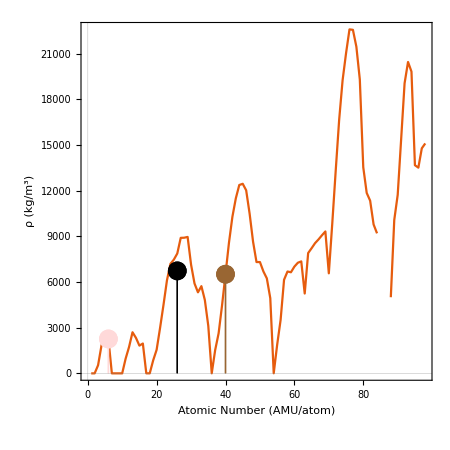

```mathematica
Show[{ListLinePlot[Table[ElementData[z,"Density"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom)",20,White],Style["ρ (kg/m^3)",20,White]},ImageSize->450,AspectRatio->1],ListPlot[Table[{z,ElementData[z,"Density"]},{z,6,6}],PlotStyle->Directive[LightRed,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[Table[{z,ElementData[z,"Density"]},{z,40,40}],PlotStyle->Directive[Brown,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[{{(12+40)/2,6.73*10^3}},PlotStyle->Directive[Black,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick]}]
```

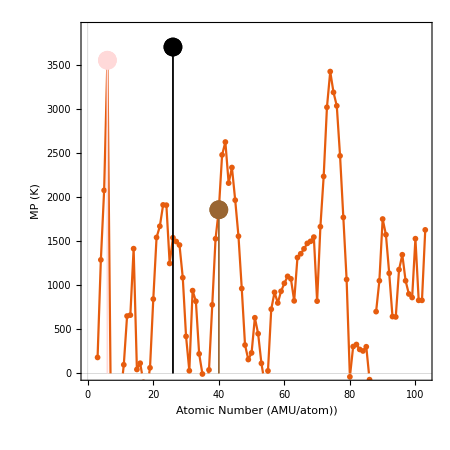

```mathematica
Show[{ListPlot[Table[ElementData[z,"MeltingPoint"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom))",20,White],Style["MP (K)",20,White]},ImageSize->450,AspectRatio->1,PlotRange->{Automatic,{0,3900}}],ListLinePlot[Table[ElementData[z,"MeltingPoint"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom)",20,White],Style["MP (K)",20,White]},ImageSize->450,AspectRatio->1,PlotRange->{Automatic,{0,3900}}],ListPlot[Table[{z,ElementData[z,"MeltingPoint"]},{z,6,6}],PlotStyle->Directive[LightRed,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[Table[{z,ElementData[z,"MeltingPoint"]},{z,40,40}],PlotStyle->Directive[Brown,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[{{(12+40)/2,(3700)}},PlotStyle->Directive[Black,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick]}]
```

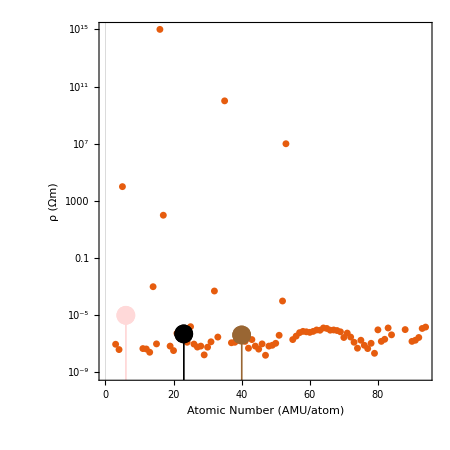

```mathematica
Show[{ListLogPlot[Table[{z,ElementData[z,"Resistivity"]},{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom)",20,White],Style["ρ (Ωm)",20,White]},ImageSize->450,AspectRatio->1],ListLogPlot[Table[{z,ElementData[z,"Resistivity"]},{z,6,6}],PlotStyle->Directive[LightRed,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListLogPlot[Table[{z,ElementData[z,"Resistivity"]},{z,40,40}],PlotStyle->Directive[Brown,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListLogPlot[{{(6+40)/2,(0.5*10^-6)}},Filling->Bottom,PlotStyle->Directive[Black,PointSize[0.03]],FillingStyle->Thick]}]
```

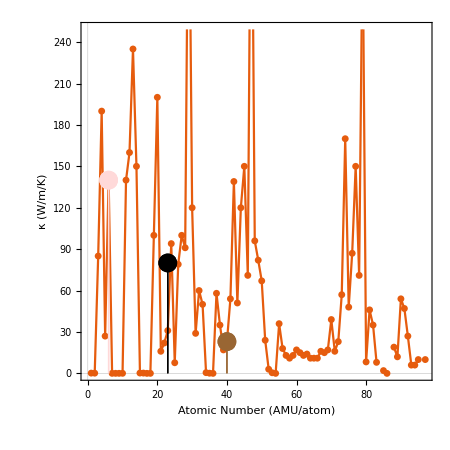

```mathematica
Show[{ListPlot[Table[ElementData[z,"ThermalConductivity"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom)",20,White],Style["κ (W/m/K)",20,White]},ImageSize->450,AspectRatio->1],ListLinePlot[Table[ElementData[z,"ThermalConductivity"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom)",20,White],Style["κ (W/m/K)",20,White]},ImageSize->450,AspectRatio->1],ListPlot[Table[{z,ElementData[z,"ThermalConductivity"]},{z,6,6}],PlotStyle->Directive[LightRed,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[Table[{z,ElementData[z,"ThermalConductivity"]},{z,40,40}],PlotStyle->Directive[Brown,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[{{(6+40)/2,(80)}},Filling->Bottom,PlotStyle->Directive[Black,PointSize[0.03]],FillingStyle->Thick]}]
```

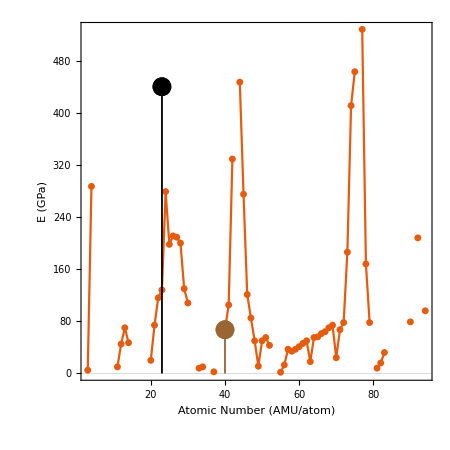

```mathematica
Show[{ListPlot[Table[ElementData[z,"YoungModulus"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom)",20,White],Style["E (GPa)",20,White]},ImageSize->450,PlotRange->All,AspectRatio->1],ListLinePlot[Table[ElementData[z,"YoungModulus"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom)",20,White],Style["E (GPa)",20,White]},ImageSize->450,PlotRange->All,AspectRatio->1],ListPlot[Table[{z,ElementData[z,"YoungModulus"]},{z,6,6}],PlotStyle->Directive[LightRed,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[Table[{z,ElementData[z,"YoungModulus"]},{z,40,40}],PlotStyle->Directive[Brown,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[{{(6+40)/2,(440)}},Filling->Bottom,PlotStyle->Directive[Black,PointSize[0.03]],FillingStyle->Thick]}]
```

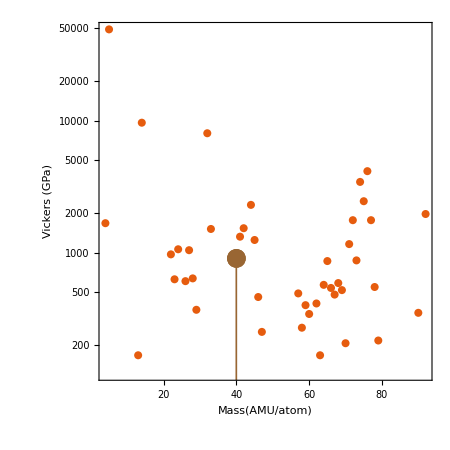

```mathematica
Show[{ListLogPlot[Table[ElementData[z,"VickersHardness"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Mass(AMU/atom)",20,White],Style["Vickers (GPa)",20,White]},ImageSize->450,PlotRange->All,AspectRatio->1],ListLogPlot[Table[{z,ElementData[z,"VickersHardness"]},{z,6,6}],PlotStyle->Directive[LightRed,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListLogPlot[Table[{z,ElementData[z,"VickersHardness"]},{z,40,40}],PlotStyle->Directive[Brown,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListLogPlot[{{(12+40)/2,(25)}},Filling->Bottom,PlotStyle->Directive[Black,PointSize[0.03]],FillingStyle->Thick]}]
```

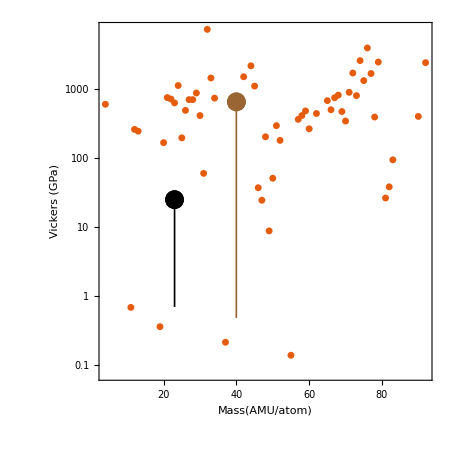

```mathematica
Show[{ListLogPlot[Table[ElementData[z,"BrinellHardness"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Mass(AMU/atom)",20,White],Style["Vickers (GPa)",20,White]},ImageSize->450,PlotRange->All,AspectRatio->1],ListLogPlot[Table[{z,ElementData[z,"BrinellHardness"]},{z,6,6}],PlotStyle->Directive[LightRed,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListLogPlot[Table[{z,ElementData[z,"BrinellHardness"]},{z,40,40}],PlotStyle->Directive[Brown,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListLogPlot[{{(6+40)/2,(25)}},Filling->Bottom,PlotStyle->Directive[Black,PointSize[0.03]],FillingStyle->Thick]}]
```

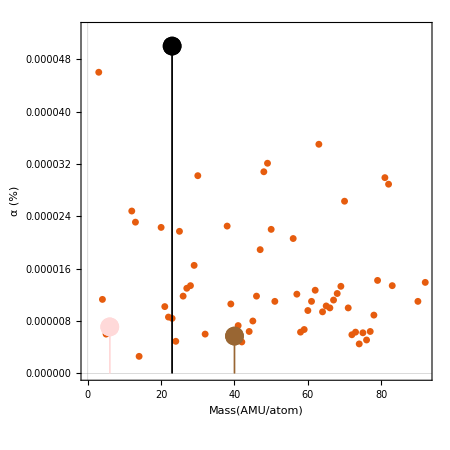

```mathematica
Show[{ListPlot[Table[ElementData[z,"ThermalExpansion"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Mass(AMU/atom)",20,White],Style["α (%)",20,White]},ImageSize->450,AspectRatio->1],ListPlot[Table[{z,ElementData[z,"ThermalExpansion"]},{z,6,6}],PlotStyle->Directive[LightRed,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[Table[{z,ElementData[z,"ThermalExpansion"]},{z,40,40}],PlotStyle->Directive[Brown,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[{{(6+40)/2,(0.00005)}},Filling->Bottom,PlotStyle->Directive[Black,PointSize[0.03]],FillingStyle->Thick]}]
```